```mathematica
(* Mathematica*)
allColors=ColorData["Legacy"][[3,1]];
firstCols=Join[{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"},{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"}];
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];(*Farey rational version:*)
```

```mathematica
Clear[f,g,ff,gg,x,ll,kk,mm]
```

```mathematica
f[x_]:=(x/(1-x))/;0<=x<=1/2
f[x_]:=((1-x)/x)/;1/2<x<=1
```

```mathematica
ff[x_]=f[Mod[Abs[x],1]]
```

f[Mod[Abs[x],1]]

```mathematica
(*second negative cycle Farey*)
```

```mathematica
g[x_]:=(x/(1-x))/;0<=x<=1/2
g[x_]:=-((1-x)/x)/;1/2<x<=1
```

```mathematica
gg[x_]=g[Mod[Abs[x],1]]
```

g[Mod[Abs[x],1]]

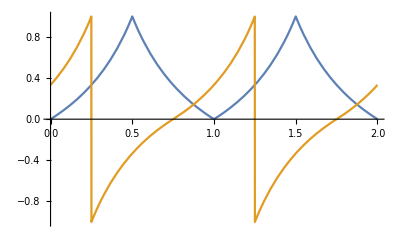

```mathematica
Plot[{ff[x],gg[x+1/4]},{x,0,2}]
```

```mathematica
Plot[ff[x],{x,0,4}];
```

```mathematica
(* dimension*)
```

```mathematica
s0=N[Log[2]/Log[3]]
```

0.63093

```mathematica
(*scale factor*)
```

```mathematica
sc=3.
```

3.

```mathematica
(*3d functions :2nd function cycled*)
```

```mathematica
kk[x_]=Sum[ff[sc^k*x]/sc^(s0*k),{k,0,20}];
ll[x_]=Sum[gg[sc^k*(x+1/4)]/sc^(s0*k),{k,0,20}];
mm[x_]=Sum[ff[sc^k*(x-1/2)]/sc^(s0*k),{k,0,20}];
```

```mathematica
digits=250000;
```

```mathematica
a0=ParallelTable[N[{ll[n/digits],kk[n/digits]}],{n,0,digits}];
```

```mathematica
g0=ListPlot[a0,AspectRatio->Automatic,ColorFunction->"Rainbow",ImageSize->2000,PlotRange->All,Background->Black,PlotStyle->PointSize[.001]];
```

```mathematica
a=ParallelTable[N[{ll[n/digits],kk[n/digits],mm[n/digits]}],{n,0,digits}];
```

```mathematica
g1=ListPointPlot3D[N[a],AspectRatio->Automatic,ColorFunction->"Rainbow",ImageSize->2000,PlotRange->All,Background->Black,ViewPoint->{2,2,2},PlotStyle->PointSize[.001]];
```

```mathematica
dlst=ParallelTable[1+Mod[Floor[1+(1+Floor[24*Norm[a[[i]]]])/(Abs[Cos[Arg[a[[i,1]]+I*a[[i,2]]]]]+Abs[Sin[Arg[a[[i,1]]+I*a[[i,2]]]]])],Length[cols]],{i,Length[a]}];
Min[dlst]
Max[dlst]

ptlst=Point[Developer`ToPackedArray[a],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

20

51

```mathematica
g2=Graphics3D[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,Axes->False,Background->Black,PlotRange->All,ViewPoint->{2,2,2}];
```

```mathematica
Export["Biscuit_Farey_cycle_scale3_3D_250000.jpg",{g0,g1,g2}]
```

Biscuit_Farey_cycle_scale3_3D_250000.jpg

```mathematica
(*end*)
```